```mathematica
ClearAll["Global`*"]
```

```mathematica
dataRaw=Mean[Import[NotebookDirectory[]<>"andResults.xlsx",{"Data",Range[1,3],All,Range@2}]];
dataRaw[[;;6,1]]=10^-10//N;
dataRaw[[;;36;;6,2]]=10^-10//N;
data=dataT=Import[NotebookDirectory[]<>"andResults.xlsx",{"Data",1,All,Range@2}];
data⟦1;;6,1⟧=10^-10;
data⟦1;;36;;6,2⟧=10^-10;
dataT⟦All,{1,2}⟧=dataT⟦All,{2,1}⟧;
```

```mathematica
(*Energy Model Fit to All Data*)
```

```mathematica
(*IPTG-Tre*)
F2D12B[i1_,i2_]:=-83.57281031521467+86688.208624169/(4.690445459252215+177.70045250507508/(1+1.7231913797211826*^6 i1^2.1596168592253027)+142.61186272142086/(1+1417.3416157628892 i2^1.1710461394326541))
(*IPTG-Rib*)
F2D13B[i1_,i2_]:=95.24754636172815+16571.78596932861/(2.5077244332838866+141.46272598182267/(1+6.547517771537234*^7 i1^2.9589910755697777)+280.70027722309266/(1+255.86758564421808 i2^1.6990615120744288))
(*Tre-Rib*)
F2D23B[i1_,i2_]:=24.146449515281017+103308.95602271675/(14.283976137089036+163.22629426654746/(1+1047.089492523756 i1^0.9887672002999788)+895.6434002583035/(1+144.2068634279749 i2^1.379475044998772))
dataModel12B=Log10[F2D12B@@@data];
dataModel13B=Log10[F2D13B@@@data];
dataModel23B=Log10[F2D23B@@@dataT];
```

```mathematica
(*Energy Model Fit to All Data*)
```

```mathematica
(*Ara-Rib*)
F2D12B[i1_,i2_]:=146.19205370324812+(149773.54826806777 (0.001436246982068665+(39.22846544885023 i1^1.8980486643959973)/(21.07625931564844+i1^1.8980486643959973)))/(1.0014362469820686+(532.9240499903088 i1^1.8980486643959973)/(21.07625931564844+i1^1.8980486643959973)+33393.840446691494/(1+42493.17827095657 i2^1.5172858831580933)+(1.6486391579413561*^7 i1^1.8980486643959973)/((21.07625931564844+i1^1.8980486643959973) (1+42493.17827095657 i2^1.5172858831580933)))
(*Ara-Tre*)
F2D13B[i1_,i2_]:=150.95696358309075+(28044.333540806394 (0.0319863547305317+(21.486676216903405 i1^1.317944748447862)/(7.653894837843844+i1^1.317944748447862)))/(1.0319863547305317+(31.440748716465624 i1^1.317944748447862)/(7.653894837843844+i1^1.317944748447862)+40053.81849968943/(1+1.2019384583777632*^6 i2^1.9863855774460188)+(398698.613230215 i1^1.317944748447862)/((7.653894837843844+i1^1.317944748447862) (1+1.2019384583777632*^6 i2^1.9863855774460188)))
(*Ara-IPTG*)
F2D14B[i1_,i2_]:=162.88130200759144+(105709.11758266758 (0.01018720654510191+(0.35157103830231823 i1^0.9272045617418939)/(2.8113531567996954+i1^0.9272045617418939)))/(1.0101872065451019+(2.0149204885864744 i1^0.9272045617418939)/(2.8113531567996954+i1^0.9272045617418939)+16.9187412651924/(1+2.7571755256837784*^16 i2^5.692760035377407)+(28.14177898295765 i1^0.9272045617418939)/((2.8113531567996954+i1^0.9272045617418939) (1+2.7571755256837784*^16 i2^5.692760035377407)))
dataModel12B=Log10[F2D12B@@@data];
dataModel13B=Log10[F2D13B@@@data];
dataModel14B=Log10[F2D14B@@@data];
```

```mathematica
sf=Log[#/0.1]/Log[10/0.1]&;
isf=InverseFunction[sf];
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

```mathematica
minmax={min,max}={10^-1,10};
```

```mathematica
vec={{0,0,165},{40,50,220},{90,120,240},{140,180,247},{195,223,240},{230,227,230},{240,223,195},{247,180,140},{240,120,90},{220,50,40},{164,0,0}};
colAll=Blend[RGBColor@@@(vec/255),Rescale[#,minmax]]&;
num=13;
opt={Frame->False,ImageSize->300,PlotRangePadding->0,DataReversed->True,ColorFunctionScaling->False,ColorFunction->colAll};
opt2={Frame->False,ImageSize->300,Frame->False,PlotRangePadding->0,ContourStyle->Directive[White,Thick]};
helv="Helvetica";
{a,b}={-4.5,1.5};
{c,d}={-4.5,1.5};
```

```mathematica
T1=Triangle[{{-4,-4.15},{2,-4.15},{2,-4.45}}];
T2=Triangle[{{-4.15,-4},{-4.15,2},{-4.45,2}}];
trian=Graphics[{EdgeForm[Thick],Black,T1,T2},ImageSize->{324,324},PlotRangePadding->0];
```

```mathematica
data=Mean[Import[NotebookDirectory[]<>"andResults.xlsx",{"Data",Range[13,15],All,4}]^2];
p1=Labeled[Overlay[{trian,{min,max}=MinMax[dataModel12B];ContourPlot[F2D12B[10^x,10^y]==(max-min)/2+min,{x,a,b},{y,c,d},Evaluate@opt2,Prolog->Inset[ArrayPlot[Transpose@Partition[data,6],Evaluate@opt]]]},Alignment->Right],{Style["IPTG (mM)",FontFamily->helv,num],Style["Trehalose (mM)",FontFamily->helv,num]},{Bottom,Left},RotateLabel->True];
```

```mathematica
data=Mean[Import[NotebookDirectory[]<>"andResults.xlsx",{"Data",Range[10,12],All,4}]^2];
p2=Labeled[Overlay[{trian,{min,max}=MinMax[dataModel13B];ContourPlot[F2D13B[10^x,10^y]==(max-min)/2+min,{x,a,b},{y,c,d},Evaluate@opt2,Prolog->Inset[ArrayPlot[Transpose@Partition[data,6],Evaluate@opt]]]},Alignment->Right],{Style["IPTG (mM)",FontFamily->helv,num],Style["Ribose (mM)",FontFamily->helv,num]},{Bottom,Left},RotateLabel->True];
```

```mathematica
data=Mean[Import[NotebookDirectory[]<>"andResults.xlsx",{"Data",Range[16,18],All,4}]^2];
p3=Labeled[Overlay[{trian,{min,max}=MinMax[dataModel23B];ContourPlot[F2D23B[10^x,10^y]==(max-min)/2+min,{x,a,b},{y,c,d},Evaluate@opt2,Prolog->Inset[ArrayPlot[Transpose@Partition[data,6],Evaluate@opt]]]},Alignment->Right],{Style["Trehalose (mM)",FontFamily->helv,num],Style["Ribose (mM)",FontFamily->helv,num]},{Bottom,Left},RotateLabel->True];
```

```mathematica
data=Mean[Import[NotebookDirectory[]<>"andResults.xlsx",{"Data",Range[4,6],All,4}]^2];
p4=Labeled[Overlay[{trian,{min,max}=MinMax[dataModel12AB];ContourPlot[F2D12AB[10^x,10^y]==(max-min)/2+min,{x,a,b},{y,c,d},Evaluate@opt2,Prolog->Inset[ArrayPlot[Transpose@Partition[data,6],Evaluate@opt]]]},Alignment->Right],{Style["Arabionose (mM)",FontFamily->helv,num],Style["Ribose (mM)",FontFamily->helv,num]},{Bottom,Left},RotateLabel->True];
```

```mathematica
data=Mean[Import[NotebookDirectory[]<>"andResults.xlsx",{"Data",Range[7,9],All,4}]^2];
p5=Labeled[Overlay[{trian,{min,max}=MinMax[dataModel13AB];ContourPlot[F2D13AB[10^x,10^y]==(max-min)/2+min,{x,a,b},{y,c,d},Evaluate@opt2,Prolog->Inset[ArrayPlot[Transpose@Partition[data,6],Evaluate@opt]]]},Alignment->Right],{Style["Arabionose(mM)",FontFamily->helv,num],Style["Trehalose (mM)",FontFamily->helv,num]},{Bottom,Left},RotateLabel->True];
```

```mathematica
data=Mean[Import[NotebookDirectory[]<>"andResults.xlsx",{"Data",Range[1,3],All,4}]^2];
p6=Labeled[Overlay[{trian,{min,max}=MinMax[dataModel14AB];ContourPlot[F2D14AB[10^x,10^y]==(max-min)/2+min,{x,a,b},{y,c,d},Evaluate@opt2,Prolog->Inset[ArrayPlot[Transpose@Partition[data,6],Evaluate@opt]]]},Alignment->Right],{Style["Arabionose (mM)",FontFamily->helv,num],Style["IPTG (mM)",FontFamily->helv,num]},{Bottom,Left},RotateLabel->True];
```

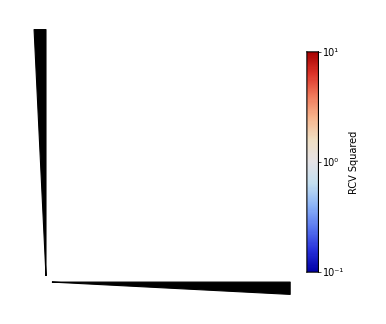
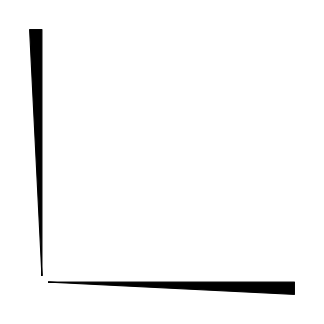
-Graphics--Graphics-IPTG (mM)Trehalose (mM) | -Graphics--Graphics-IPTG (mM)Ribose (mM) | -Graphics--Graphics-Trehalose (mM)Ribose (mM) | -Graphics--Graphics-Arabionose (mM)Ribose (mM) | -Graphics--Graphics-Arabionose(mM)Trehalose (mM) | -Graphics--Graphics-Arabionose (mM)IPTG (mM)

```mathematica
RCV=Legended[Multicolumn[Table[Symbol["p"<>ToString[i]],{i,6}],6,Appearance->"Horizontal"],BarLegend[{colAll,minmax},ScalingFunctions->{sf,isf},LegendMarkerSize->{30,350},"TickLengths"->3,"TicksStyle"->Directive[Opacity[1],Black],Ticks->{{0.1,Superscript[10,-1]},{1,Superscript[10,0]},{10,Superscript[10,1]}},LabelStyle->Directive[FontSize->22],LegendLabel->Placed[Style["RCV Squared",18],Right,Rotate[#,90Degree]&]]]
```

```mathematica
Export[NotebookDirectory[]<>"EnergyFigure4.PDF",RCV];
```